```mathematica
(* MA39110 / Assignment 1 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=1;xf=1.4;h=(xf-x0)/n;
y0=0;yf=0.0566;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X =Table[x0+x*h,{x,1,n-1}];
B =Table[2*h^2,{x,1,n-1}];
For[i=1,i<n,i++,
{
A[[i,i]]=-4*X[[i]]^2;
If[i≠1,A[[i,i-1]]=2*X[[i]]^2-h*X[[i]]];
If[i≠n-1,A[[i,i+1]]=2*X[[i]]^2+h*X[[i]]];
}];
B[[1]]-=y0*(2*X[[1]]^2-h*X[[1]]);
B[[n-1]]-=yf*(2*X[[n-1]]^2+h*X[[n-1]]);
Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B]];
```

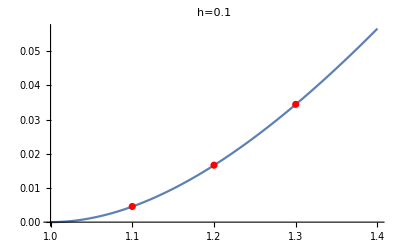

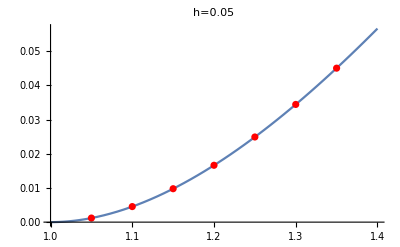

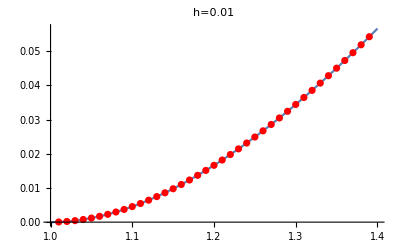

```mathematica
sol=Model[4];
Show[{Plot[0.5*Log[x]^2,{x,x0,xf},PlotLabel->Style["h=0.1",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}]
sol=Model[8];
Show[{Plot[0.5*Log[x]^2,{x,x0,xf},PlotLabel->Style["h=0.05",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}]
sol=Model[40];
Show[{Plot[0.5*Log[x]^2,{x,x0,xf},PlotLabel->Style["h=0.01",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}]
```